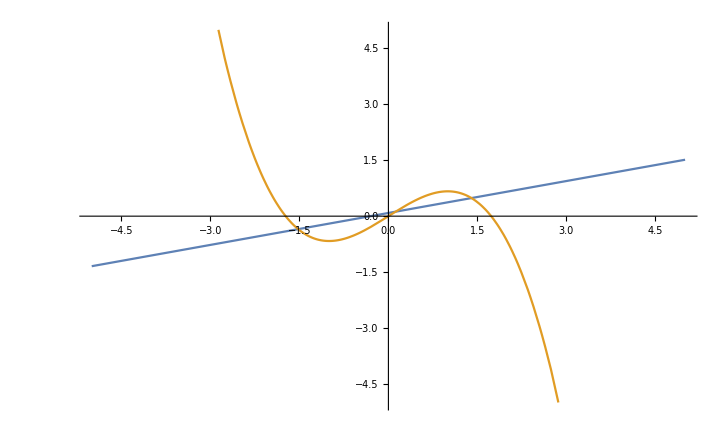

```mathematica
b = 0.3;
g = 3.5;
f[u_] := (u+b)/g;
h[u_] := u-(u^3)/3;
Plot[{f[u],h[u]},{u,-5,5},PlotRange->{-5,5}]
```

```mathematica
Solve[f[u] == h[u],u]
```

{{u→-1.52052},{u→0.120823},{u→1.39969}}

```mathematica
f[-1.5205171923724354]
```

-0.348719

```mathematica
h[-1.5205171923724354]
```

-0.348719

```mathematica
f[1.3996940844350543]
```

0.485627

```mathematica
h[1.3996940844350543]
```

0.485627